Тема 12. Застосування інтегрального числення.

Завдання 1. Обчислення площі між двома кривими, які задані явно.

Використовуючи систему «Mathematica», обчислити площу області, яка обмежена графіками функцій між точками їх перетинання. Зобразити графіки функцій та зону, площа якої обчислюється.

```mathematica
y1[x_]=x^2-7*x-2;
y2[x_]=3*x^2+3*x-14;
s=Solve[y1[x]==y2[x],x,Reals]
```

{{x→-6},{x→1}}

```mathematica
x1=x/.s[[1]]
```

-6

```mathematica
x2=x/.s[[2]]
```

1

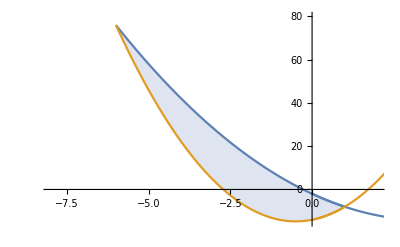

```mathematica
p1=Plot[{y1[x],y2[x]},{x,0,4},PlotRange->{{-8,2},{-15,80}}];
p2=Plot[{y1[x],y2[x]},{x,x1,x2},Filling->{1->{2}}];
Show[p1,p2]
```

```mathematica
Integrate[y1[x]-y2[x],{x,x1,x2}]
```

343/3

Завдання 2. Обчислення довжини кривої, яка задана явно.

Використовуючи систему «Mathematica», обчислити довжину відрізка кривої, рівняння якої задано в явному вигляді. Побудувати графік кривої та криволінійного відрізка, довжина якого обчислюється. Діапазон зміни абсцис графіка підбирати самостійно.

```mathematica
Replace[x]
```

Replace[x]

```mathematica
y[x_]=Log[5/(2*x)];
x1=√3;
x2=√8;
L=∫_x1^x2 √(1+y'[x]^2)ⅆx
```

1+ArcTanh[2]-ArcTanh[3]

```mathematica
N[L]
```

1.20273+0. ⅈ

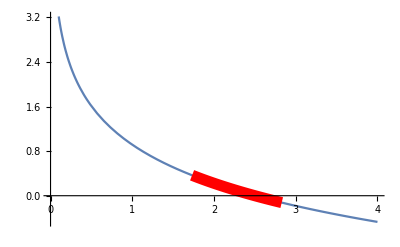

```mathematica
p1=Plot[y[x],{x,0,4}];
p2=Plot[y[x],{x,x1,x2},PlotStyle->{Thickness[0.02],Red}];
Show[p1,p2]
```

Завдання 3. Обчислення довжини параметричної кривої.

Використовуючи систему «Mathematica», обчислити довжину відрізка кривої, яка задана параметричними рівняннями. Побудувати графік криволінійного відрізка, довжина якого обчислюється.

```mathematica
x[t_]=(t^2-2)*Sin[t]+2*t*Cos[t];
y[t_]=(2-t^2)*Cos[t]+2*t*Sin[t];
Tmin=0; Tmax=4*π;
L=Integrate[√(D[x[t],t]^2+D[y[t],t]^2),{t,Tmin,Tmax}]
```

(64 π^3)/3

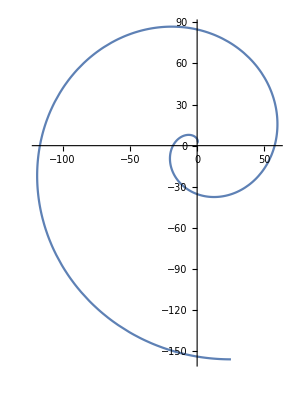

```mathematica
ParametricPlot[{x[t],y[t]},{t,Tmin,Tmax}]
```

Завдання 4. Обчислення маси платівки.

Дано поверхневу густину платівки μ(x, y) і задано область, яку вона займає на площині. Зобразити платівку та знайти її масу.

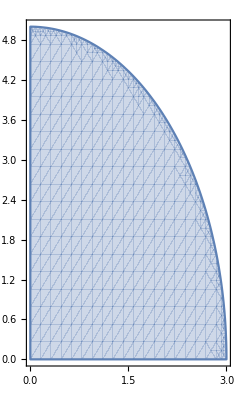

```mathematica
R=x^2/9+y^2/25<=1&&y>=0;
RegionPlot[R,{x,0,3},{y,0,5},AspectRatio->Automatic]
```

```mathematica
mu[x_,y_]=7*x^2*y/18;
M=Integrate[mu[x,y]*Boole[R],{x,0,3},{y,0,5}]
```

35/2

Завдання 5. Обчислення об’єму тіла.

Знайти об’єм тіла, яке задано нерівностями. Побудувати зображення тіла.

```mathematica
R = (4<=x^2+y^2+z^2<=36)&&(0<=y<=x/√3)&&(-√((x^2+y^2)/63)<=z);
RegionPlot3D[R,{x,0,6},{y,0,3},{z,0,6},PlotPoints->100,Boxed->False,AxesOrigin->{0,0,0},Mesh->None]
```

-Graphics3D-

```mathematica
Chop[NIntegrate[Boole[R],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]]
```

40.8407